#### Specialization Program

This function specializes a graph object ”G0” over a specified list of vertex indices, “list” (vertex indices in the list correspond to vertices which remain fixed by the expansion process).  The new specialized graph is labeled  “NEW.” Note that the elements in list are not the names of the vertices, they are the corresponding indices.  These two types of lists are the same if you first use the command “IndexGraph” on your Graph. ( “IndexGraph” takes in a Graph object for its input and outputs a graph object whose vertices are named by their index). Also note that the names of the fixed vertices are changed in NEW. The default for “list” is the first single vertex.  (If this vertex is not contained in any cycles, the expansion will not result in an empty graph, since the graph is built out of connection to other vertices in “list.”)

```mathematica
Specialize[G0_,list_ :{1}]:=Module[{G=G0,u=list,A,cc,ou,o,in,out,connect1,connect,connectout,pathlist,k,q,l,uo,na1,place,size,w,e,ki,el,currentco,naa2,cuurentcomp,naa},G=DirectedGraph[G];A=AdjacencyMatrix[G];
cc=ConnectedComponents[VertexDelete[G,u]];
ou=Flatten[cc];
o=ArrayRules[A];
in=Part[#,1]&/@Delete[Select[o,(MemberQ[u,#[[1,1]]]&&MemberQ[ou,#[[1,2]]])&],-1];
out=Part[#,1]&/@Delete[Select[o,(MemberQ[u,#[[1,2]]]&&MemberQ[ou,#[[1,1]]])&],-1];
connect1=Part[#,1]&/@Delete[Select[o,(MemberQ[ou,#[[1,2]]]&&MemberQ[ou,#[[1,1]]])&],-1];
connect=Select[connect1,(Position[cc,#[[1]]][[1,1]]≠Position[cc,#[[2]]][[1,1]])&];
connectout=Join[connect,out];
pathlist={};
For[i=1,i≤Length[in],i++,
pathlist=Append[pathlist,{in[[i]]}];k=1;
While[k≤Length[pathlist],link=(Last@pathlist[[k]])[[2]];If[MemberQ[u,link],k++,
currentcomp=cc[[Position[cc,link][[1,1]]]];newedges={};
For[q=1,q≤ Length[connectout],q++,If[MemberQ[currentcomp,connectout[[q,1]]],newedges=Append[newedges,connectout[[q]]]]];For[l=1,l≤Length[newedges],l++,pathlist=Append[pathlist,Append[pathlist[[k]],newedges[[l]]]]];pathlist=Delete[pathlist,k];
]]];
uo=EdgeList[Subgraph[G,u]];
na1={};
place=1;size=VertexCount[G];
For[w=1,w≤ Length[pathlist],w++,add={};
For[e=1,e≤Length[pathlist[[w]]],e++,
If[e==Length[pathlist[[w]]],piece={pathlist[[w,e,1]]+place*size,pathlist[[w,e,2]]};add=Append[add,piece],
ki=pathlist[[w,e,2]];
currentco=Select[cc,MemberQ[#,ki]&][[1]];
el=EdgeList[Subgraph[G,currentco]];
el={#[[1]],#[[2]]}&/@el+place*size;
If[el≠{},add=Append[add,el]];
If[e==1,piece={pathlist[[w,e,1]],pathlist[[w,e,2]]+place*size},piece=pathlist[[w,e]]+place*size];add=Append[add,piece]
]];place++;na1=Append[na1,add]];
naa2=(#[[1]]->#[[2]])&/@Partition[Flatten[na1],2];naa=Join[uo,naa2];
NEW=IndexGraph[naa]]
```

#### Example

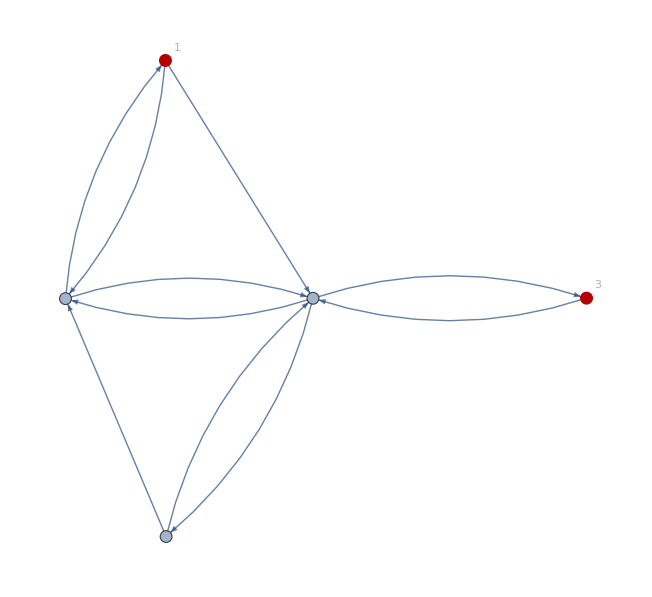

```mathematica
G=Graph[-Graphics-,GraphLayout->"SpringEmbedding"]; (*Define a graph*)
G=IndexGraph[G]; (*Reindex the vertices*)
HighlightGraph[G,{1,3},VertexLabels->Automatic](*Highlighted Red nodes are the two we are specializing over (1,6)*)
```

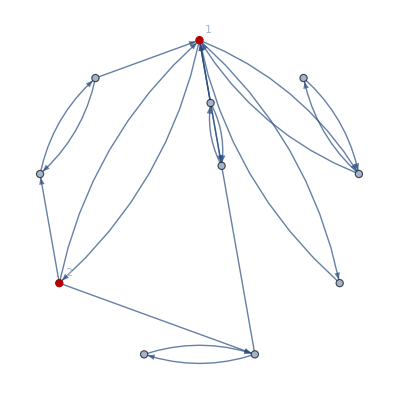

```mathematica
Specialize[G,{4,5}]; (*Specialize command take the Graph object for its first argument, and list of vertices to remain fixed as its second*)
HighlightGraph[Graph[NEW,GraphLayout->"TutteEmbedding"],{1,2},VertexLabels->Automatic] (*Note here that the specialized graph is called "NEW". Red nodes are the fixed nodes from the previous step (Note that vertex 1 was relabled as 5)*)
```